## LOAD DATA

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
hyperedges=Import["Picasso/H.dat","Data"]
```

{{1},{2},{1,2},{3},{1,3},{4},{1,4},{2,4},{1,2,4},{3,4},{5},{1,5},{2,5},{3,5},{1,3,5},{6},{1,6},{3,6},{1,3,6},{5,6},{1,5,6},{7},{1,7},{3,7},{4,7},{1,4,7}}

```mathematica
Interpreter[DelimitedSequence["Number"]][#]&/@hyperedges
```

{{Failure[…]},{Failure[…]},{{1,2}},{Failure[…]},{{1,3}},{Failure[…]},{{1,4}},{{2,4}},{{1,2,4}},{{3,4}},{Failure[…]},{{1,5}},{{2,5}},{{3,5}},{{1,3,5}},{Failure[…]},{{1,6}},{{3,6}},{{1,3,6}},{{5,6}},{{1,5,6}},{Failure[…]},{{1,7}},{{3,7}},{{4,7}},{{1,4,7}}}

## VISUALIZATION

```mathematica
temp=hyperedges⟦9⟧
```

{1,2,4}

```mathematica
temp⟦1⟧
temp⟦2⟧
```

1,2,4

Part::partw: Part 2 of {1,2,4} does not exist.

{1,2,4}⟦2⟧

```mathematica
ToExpression[RowBox["1,2"]]
```

ToExpression::esntx: Could not parse RowBox[1,2] as input.

$Failed

```mathematica
Interpreter[DelimitedSequence["Number"]]["{1}"]
```

Failure[…]

```mathematica
Length⟦#⟧&/@hyperedges
```

Part::partd: Part specification Length⟦{1}⟧ is longer than depth of object.

Part::partd: Part specification Length⟦{2}⟧ is longer than depth of object.

Part::partd: Part specification Length⟦{1,2}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{Length⟦{1}⟧,Length⟦{2}⟧,Length⟦{1,2}⟧,Length⟦{3}⟧,Length⟦{1,3}⟧,Length⟦{4}⟧,Length⟦{1,4}⟧,Length⟦{2,4}⟧,Length⟦{1,2,4}⟧,Length⟦{3,4}⟧,Length⟦{5}⟧,Length⟦{1,5}⟧,Length⟦{2,5}⟧,Length⟦{3,5}⟧,Length⟦{1,3,5}⟧,Length⟦{6}⟧,Length⟦{1,6}⟧,Length⟦{3,6}⟧,Length⟦{1,3,6}⟧,Length⟦{5,6}⟧,Length⟦{1,5,6}⟧,Length⟦{7}⟧,Length⟦{1,7}⟧,Length⟦{3,7}⟧,Length⟦{4,7}⟧,Length⟦{1,4,7}⟧}

```mathematica
g=Graph3D[{1<->2,2<->3,3<->1,4<->1,4<->3,4<->2,5<->1,6<->5,7<->5,7<->6,8<->6,9<->6},VertexLabels->"Name",BaseStyle->Darker@Gray,EdgeStyle->Lighter@Blue,VertexSize->Small]
AbsoluteOptions[g,VertexCoordinates];

𝒫=Polyhedron[{{0.,0.,0.6},{-0.3,-0.5,-0.2},{-0.3,0.5,-0.2},{0.6,0.,-0.2}},{{2,3,4},{3,2,1},{4,1,2},{1,4,3}}];
```

-Graphics3D-

```mathematica
g=Graph3D[{1<->2,2<->3,3<->1,4<->1,4<->3,4<->2,5<->1,5<->4,6<->2,7<->6,8<->6},VertexLabels->"Name",BaseStyle->Darker@Gray,EdgeStyle->Lighter@Blue,VertexSize->Small]
```

```mathematica
Export["img1.svg",-Graphics3D-]
```

```mathematica
Export["out.pdf",Graphics[Inset[-Graphics3D-],ImageSize->100]]
```

out.pdf

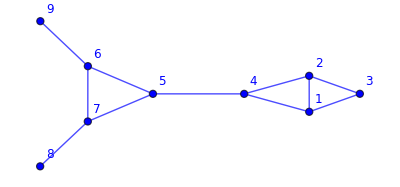

```mathematica
Graph[{1<->2,2<->3,1<->3,4<->1,4<->2,5<->4,6<->5,7<->5,6<->7,8<->7,9<->6},
VertexLabelStyle->Directive[12],
VertexLabels->"Name",BaseStyle->Blue,VertexSize->Medium]
```

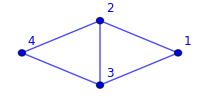

```mathematica
Graph[{1<->2,2<->3,1<->3,3<->4,2<->4},
VertexLabelStyle->Directive[12],
ImageSize->200,
VertexLabels->"Name",BaseStyle->Blue,VertexSize->Small]
```

## Mobius

```mathematica
mobiusEdges ={
1<->2,1<->3,1<->6,
2<->3,2<->4,2<->6,2<->5,
3<->4,3<->5,
4<->5,4<->6,
5<->6
};

mobiusHyperedges = {{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,2},{1,6,2}};

g3d=Graph3D[Range[1,6],mobiusEdges,VertexLabels->"Name",BaseStyle->Darker@Gray,EdgeStyle->Lighter@Blue,VertexSize->Small];

coordinates=GraphEmbedding@g3d;

hyperedgecoordinates = coordinates⟦#⟧&/@mobiusHyperedges;

Show[
Table[
Graphics3D[{Lighter@Blue,Opacity[0.9],Triangle[coords]}]
,{coords,hyperedgecoordinates}],
g3d,
ImageSize->500
]
```

-Graphics3D-

-Graphics3D-

## Hypergraph Picasso

```mathematica
hyperedges
```

{{1},{2},{1,2},{3},{1,3},{4},{1,4},{2,4},{1,2,4},{3,4},{5},{1,5},{2,5},{3,5},{1,3,5},{6},{1,6},{3,6},{1,3,6},{5,6},{1,5,6},{7},{1,7},{3,7},{4,7},{1,4,7}}

```mathematica
edges ={
1<->2,1<->3,1<->4,2<->4,3<->4,1<->5,2<->5,3<->5,1<->6,3<->6,5<->6,1<->7,3<->7,4<->7
};

hyperedges={{1,2,4},{1,3,5},{1,3,6},{1,5,6},{1,4,7}};

g3d=Graph3D[Range[1,7],edges,
VertexLabels->"Name",
BaseStyle->Darker@Gray,
EdgeStyle->Lighter@Blue,
VertexSize->Small,
(*GraphLayout-> "HighDimensionalEmbedding"*)
GraphLayout->"SpringElectricalEmbedding"
];

coordinates=GraphEmbedding@g3d;
hyperedgecoordinates = coordinates⟦#⟧&/@hyperedges;

Show[
Table[
Graphics3D[{Blue,Opacity[0.5],Simplex[coords]}]
,{coords,hyperedgecoordinates}],
g3d,
Boxed->False,
ImageSize->400
]
```

-Graphics3D-